```mathematica
a=Import["/Users/stevenschowalter/desktop/mms2-10.txt","Data"];
```

```mathematica
b= Drop[a,2];
```

```mathematica
c= Flatten[Take[b,All,-1]];
```

```mathematica
{num}=Dimensions[c]
```

{3214}

```mathematica
step=.2;
k=0;
x=1;
```

```mathematica
stoop=Table[0,{i,20/step}];
```

```mathematica
Do[
{
Do[
If[c[[i]]≥k*step&&c[[i]]<(k+1)*step,
{
x++;
}
],{i,1,num}];
stoop[[k+1]]={(2k+1)/2*step,x};
x=0;
}
,{k,0,20/step-1}
]
```

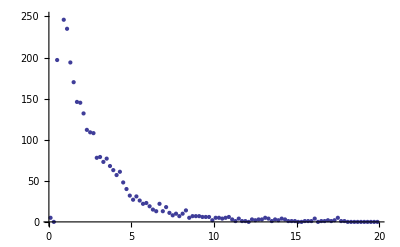

```mathematica
datpl=ListPlot[stoop,PlotRange->{0,250}]
```

```mathematica
fit=FindFit[Drop[Drop[stoop,2],-10],aa ⅇ^(-bb t),{aa,bb},t]
```

{aa→341.543,bb→0.44913}

```mathematica
fitpl=Plot[aa ⅇ^(-bb t)/.fit,{t,0,20},PlotRange->All,PlotStyle->{Red,Thickness[.01]}];
```

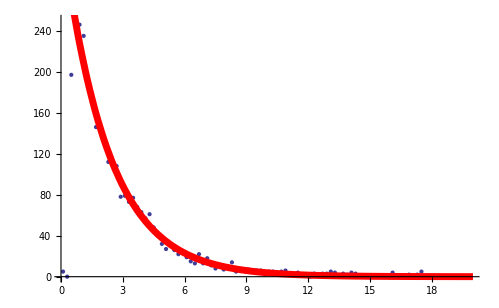

```mathematica
Show[datpl,fitpl]
```

```mathematica
(bb/.fit)^-1
```

2.22653

```mathematica
Needs["NonlinearRegression`"]
```

```mathematica
weight=Table[√(stoop[[i]][[2]])//N,{i,100}] ;
```

```mathematica
dat=Drop[Drop[stoop,2],-10];
weights=Drop[Drop[weight,2],-10];
```

```mathematica
NonlinearRegress[dat,gg ⅇ^(- t/τ),{gg,τ},t,Weights->weights]
```

{BestFitParameters→{gg→347.434,τ→2.21629},ParameterCITable→ | Estimate | Asymptotic SE | CI
gg | 347.434 | 11.1502 | {325.268,369.6}
τ | 2.21629 | 0.100696 | {2.01612,2.41647},EstimatedVariance→2026.23,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 6.2656×10^6 | 3.1328×10^6
Error | 86 | 174255. | 2026.23
Uncorrected Total | 88 | 6.43985×10^6 | 
Corrected Total | 87 | 3.04948×10^6 | ,AsymptoticCorrelationMatrix→(1. | -0.828263
-0.828263 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0.186458
Max Parameter-Effects | 0.654278
95. % Confidence Region | 0.567728}